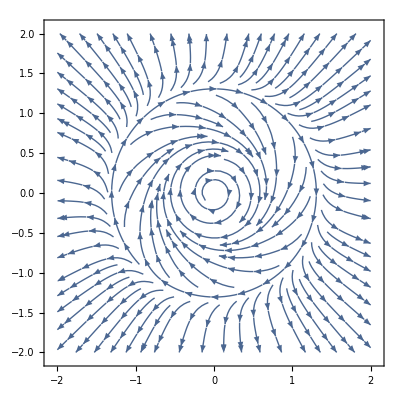

```mathematica
(* 1 Plot for μ=0.5 *)
StreamPlot[Evaluate@TransformedField["Polar"->"Cartesian",{(r^4-2*r^2+0.5)*r,-1},{r,θ}->{x,y}],{x,-2,2},{y,-2,2}]
```

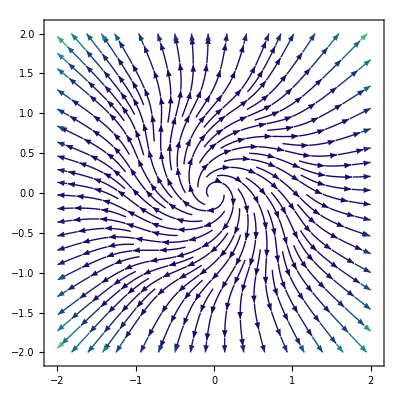

```mathematica
(* 1 Plot for μ=2 *)
StreamPlot[Evaluate@TransformedField["Polar"->"Cartesian",{(r^4-2*r^2+2)*r,-1},{r,θ}->{x,y}],{x,-2,2},{y,-2,2},StreamColorFunction->"BlueGreenYellow"]
```

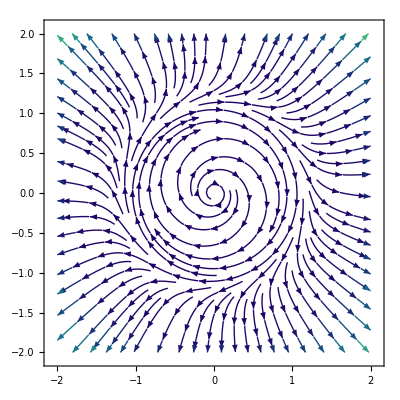

```mathematica
(* 1 Plot for μ=2 *)
StreamPlot[Evaluate@TransformedField["Polar"->"Cartesian",{(r^4-2*r^2+1)*r,-1},{r,θ}->{x,y}],{x,-2,2},{y,-2,2},StreamColorFunction->"BlueGreenYellow"]
```

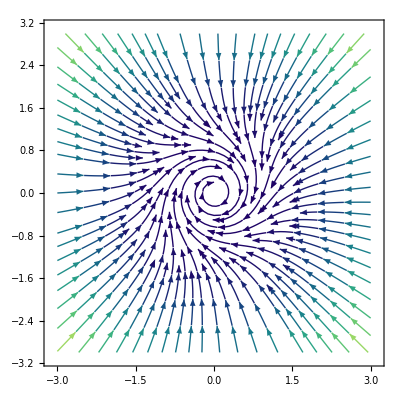

```mathematica
(* 2 Plot for μ=0.5 *)
StreamPlot[Evaluate@TransformedField["Polar"->"Cartesian",{-0.5*r+r^2-r^3,-1},{r,θ}->{x,y}],{x,-3,3},{y,-3,3},StreamColorFunction->"BlueGreenYellow"]
```

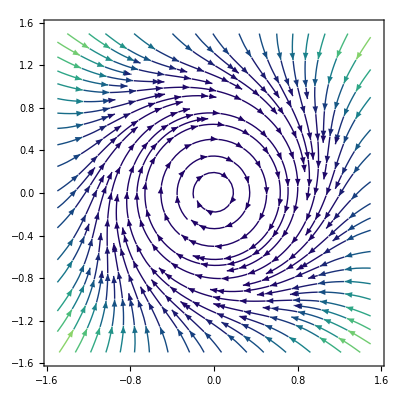

```mathematica
(* 2 Plot for μ=0.25 *)
StreamPlot[Evaluate@TransformedField["Polar"->"Cartesian",{-0.25*r+r^2-r^3,-1},{r,θ}->{x,y}],{x,-1.5,3/2},{y,-3/2,3/2},StreamColorFunction->"BlueGreenYellow"]
```

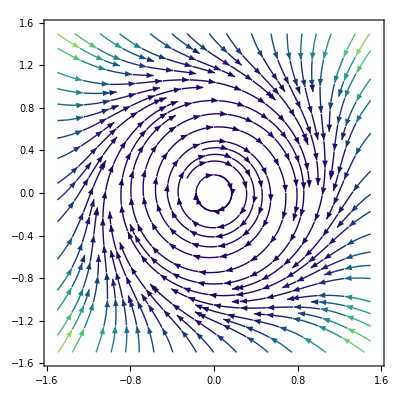

```mathematica
(* 2 Plot for μ=0.125 *)
StreamPlot[Evaluate@TransformedField["Polar"->"Cartesian",{-0.125*r+r^2-r^3,-1},{r,θ}->{x,y}],{x,-1.5,3/2},{y,-3/2,3/2},StreamColorFunction->"BlueGreenYellow"]
```

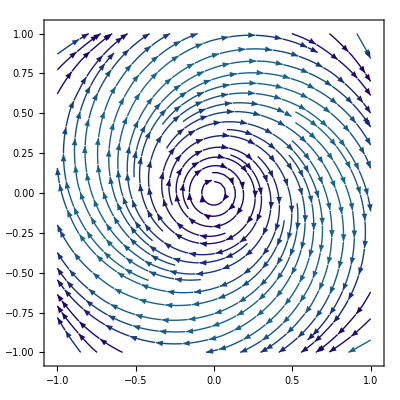

```mathematica
(* 2 Plot for μ=-0.25 *)
StreamPlot[Evaluate@TransformedField["Polar"->"Cartesian",{0.25*r+r^2-r^3,-1},{r,θ}->{x,y}],{x,-1,1},{y,-1,1},StreamColorFunction->"BlueGreenYellow"]
```

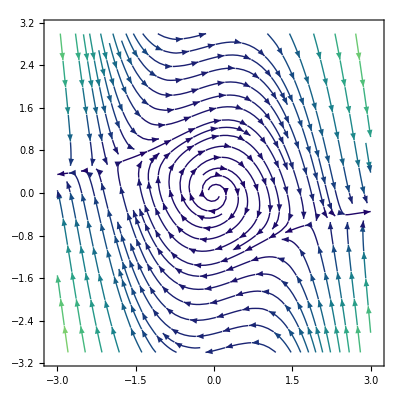

```mathematica
(* 3a Plot for μ=0.25 *)
StreamPlot[{y+0.25*x,-x+0.25*y-x^2*y},{x,-3,3},{y,-3,3},StreamColorFunction->"BlueGreenYellow"]
```

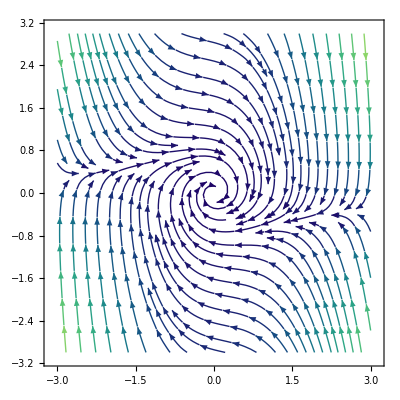

```mathematica
(* 3a Plot for μ=-0.25 *)
StreamPlot[{y-0.25*x,-x-0.25*y-x^2*y},{x,-3,3},{y,-3,3},StreamColorFunction->"BlueGreenYellow"]
```

```mathematica
(* Hence 3a is a Supercritical Hopf Bifurcation *)
```

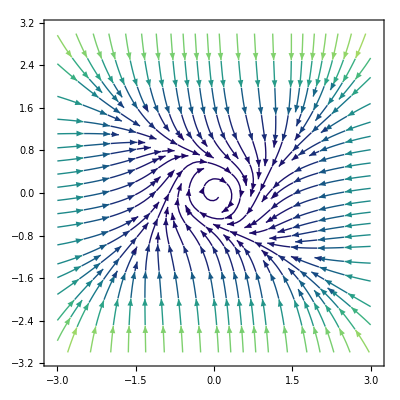

```mathematica
(* 3b Plot for μ=0.25 *)
StreamPlot[{y+0.25*x-x^3,-x+0.25*y-2*y^3},{x,-3,3},{y,-3,3},StreamColorFunction->"BlueGreenYellow"]
```

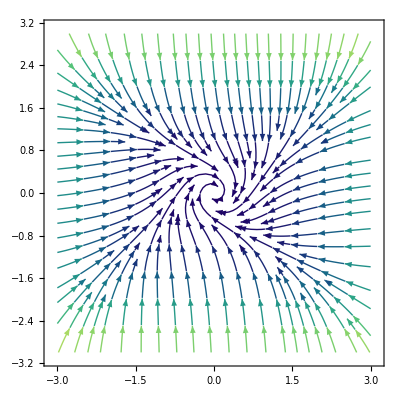

```mathematica
(* 3b Plot for μ=-0.25 *)
StreamPlot[{y-0.25*x-x^3,-x-0.25*y-2*y^3},{x,-3,3},{y,-3,3},StreamColorFunction->"BlueGreenYellow"]
```

```mathematica
(* Hence 3b is a Supercritical Hopf Bifurcation *)
```

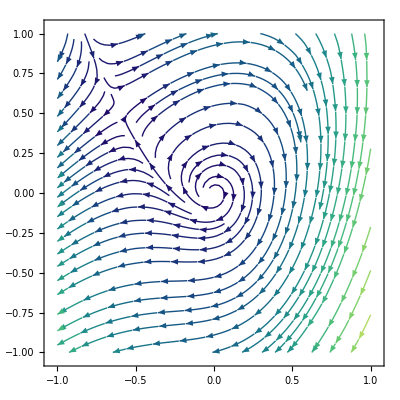

```mathematica
(* 3c Plot for μ=0.25 *)
StreamPlot[{y+0.25*x-x^2,-x+0.25*y-2*x^2},{x,-1,1},{y,-1,1},StreamColorFunction->"BlueGreenYellow"]
```

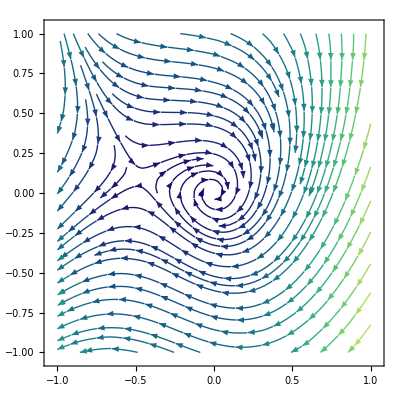

```mathematica
(* 3c Plot for μ=-0.25 *)
StreamPlot[{y-0.25*x-x^2,-x-0.25*y-2*x^2},{x,-1,1},{y,-1,1},StreamColorFunction->"BlueGreenYellow"]
```

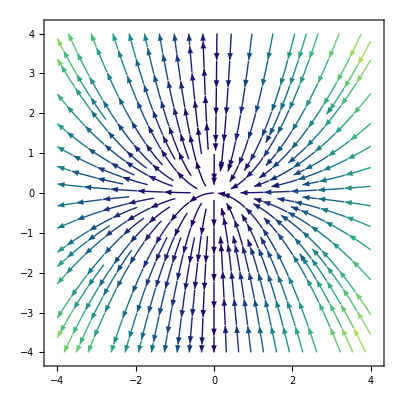

```mathematica
(* Hence 3c is a Subcritical Hopf Bifurcation *)

(* For Assignment 7 Problem 2 *)

(* μ= 0 *)

StreamPlot[{-x^2,y*(-2*x)},{x,-4,4},{y,-4,4},StreamColorFunction->"BlueGreenYellow"]
```